## Matrix elements for the single-particle Hamiltonian h

Fromula:-Graphics-

Taken from: -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
A=167;
j1=13/2;
j2=11/2;
coupling[j_,beta_]:=195/(j(j+1))A^(-1/3)beta;
hdiag[j_,k_,beta_,gamma_]:=1/2 coupling[j,beta]*Cos[gamma*π/180](k^2-1/3 j(j+1));
```

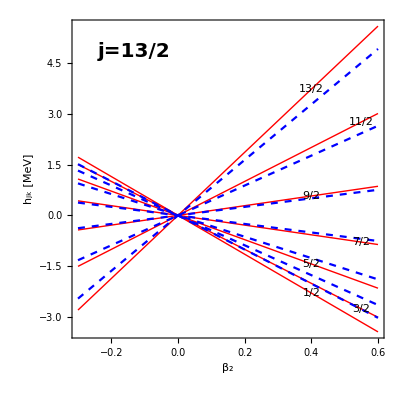

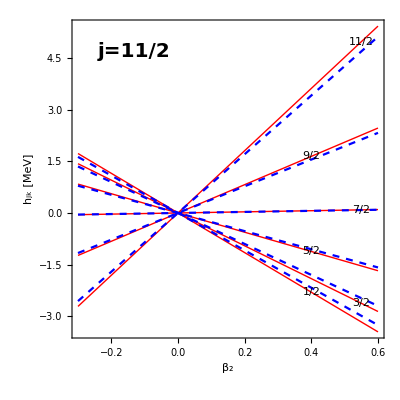

```mathematica
(*use Evaluate to apply different colors to the table lines*)
betaPlot[j_,gamma_]:=Plot[Table[hdiag[j,k,x,gamma],{k,1/2,j,1}],{x,-0.3,0.6},AspectRatio->1,Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],AxesStyle->Directive[Black,Dashed],PlotStyle->Directive[Red,Thick],(*PlotLegends->Table[StringTemplate["k=(``)/2"][2k],{k,1/2,j,1}],*)(*PlotLegends->Placed[SwatchLegend[Table[StringTemplate["k=(``)/2"][2k],{k,1/2,j,1}],LegendLabel->None,LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,DotDashed,Thin]]&)],Automatic]*)LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"β_2","h_jk [MeV]"},Epilog->{Table[Inset[Framed[Style[StringTemplate["``/2"][2k],Black,13,Bold],Background->White,FrameStyle->None],{0.4,hdiag[j,k,0.4,gamma]}],{k,1/2,j,2}],Table[Inset[Framed[Style[StringTemplate["``/2"][2k],Black,13,Bold],Background->White,FrameStyle->None],{0.55,hdiag[j,k,0.55,gamma]}],{k,3/2,j,2}],Inset[Style[StringTemplate["j=``/2"][2j],Black,20,Bold],Scaled[{0.2,0.9}]]},PlotLegends->Placed[{StringTemplate["γ=(``)^o"][gamma]},Scaled[{0.2,0.7}]]];
betaPlot2[j_,gamma_]:=Plot[Table[hdiag[j,k,x,gamma],{k,1/2,j,1}],{x,-0.3,0.6},AspectRatio->1,Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],AxesStyle->Directive[Black,Dashed],PlotStyle->Directive[Blue,Dashed],(*PlotLegends->Table[StringTemplate["k=(``)/2"][2k],{k,1/2,j,1}],*)(*PlotLegends->Placed[SwatchLegend[Table[StringTemplate["k=(``)/2"][2k],{k,1/2,j,1}],LegendLabel->None,LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,DotDashed,Thin]]&)],Automatic]*)LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"β_2","h_jk [MeV]"},PlotLegends->Placed[{StringTemplate["γ=(``)^o"][gamma]},Scaled[{0.2,0.7}]]];
f1=Show[betaPlot[j1,10],betaPlot2[j1,30]];
f2=Show[{betaPlot[j2,5],betaPlot2[j2,20]}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/quadrupole-deformed-potential/singleParticle-hdiag-1.pdf",f1];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/quadrupole-deformed-potential/singleParticle-hdiag-2.pdf",f2];
f1
f2
```